# Math Boot Camp: Coordinate Systems

You can skip this boot camp if you can answer the following question:

Example
Staying on a sphere of radius R, what is the shortest distance between the point (0,0,R) on the z-axis and a general point (x,y,z) on the sphere?

```mathematica
θ=0.6;
colors={RGBColor[0, 0.38, 0.1],RGBColor[0, 0.52, 1]};
pnts=Table[1.05{Sin[θθ],0,Cos[θθ]},{θθ,0,θ,0.01}];
centerPlot@Graphics3D[{Sphere[],PointSize[0.02],{colors[[1]],Point[1.05{{0,0,1},{Sin[θ],0,Cos[θ]}}]},{colors[[2]],Line[pnts]},Text[font["(0,0,R)"],{0,0,1.3}],Text[font["(x,y,z)"],1.3{Sin[θ],0,Cos[θ]}+{0.1,0,0}]},Boxed->False,PlotRangePadding->None,ImageSize->{151.24999999999815,168.75},PlotRangePadding->None,ViewAngle->0.28134970767492745]
```

-Graphics3D-

### 2D Polar Coordinates

A generic 2D vector in Cartesian coordinates is

A⃗=A_x x̂+A_y ŷ

which in polar coordinates equals

A⃗=r Cos[θ]x̂+r Sin[θ]ŷ

where

r=√(A_x^2+A_y^2)

θ=ArcTan[A_y/A_x]

```mathematica
arc[r_,{θ1_,θ2_}]:=
If[θ1==θ2,{},Line[Table[r{Cos[θ],Sin[θ]},{θ,θ1,θ2,((θ2-θ1)/50.)}]]]
centerPlot@Manipulate[With[{label=1.3},
Graphics[{
{RGBColor[1, Rational[12, 17], Rational[6, 17]],Disk[{0,0},1]},
Arrowheads[Medium],
Arrow[1.2{{{-1,0},{1,0}},{{0,-1},{0,1}}}],
Text[font["x",14,Italic],label{1,0}],
Text[font["y",14,Italic],label{0,1}],
With[{θ=If[pnt[[2]]==0,0,Mod[ArcTan@@pnt,2π]],len=2Norm[pnt],ar=.15,tr=.22},
{
arc[ar,{0,θ}],
{Thick,RGBColor[0.32, 0., 0.51],Arrow[{{0,0},pnt}]},
Text[font["θ",12],tr {Cos[θ/2], Sin[θ/2]}],
Text[font["r",12,Italic],len{Cos[θ]/4,Sin[θ]/4}+{-0.06,0.06}],Text[font["A_x",12],{len Cos[θ]/4,-0.1}],
Text[font["A_y",12],{-0.1,len Sin[θ]/4}],
Dashed,Line[len{{{Cos[θ]/2,0},{Cos[θ]/2,Sin[θ]/2}},{{0,Sin[θ]/2},{Cos[θ]/2,Sin[θ]/2}}}],{FaceForm[],EdgeForm[{Thick,color1}],Rectangle[{-1.4,0.88},{-0.6,1.52}]},Text[font["Cartesian",Bold,12],{-1,1.4}],Text[font["A_x = "<>ToString@Round[len Cos[θ],0.1],12],{-1,1.2}],Text[font["A_y = "<>ToString@Round[len Sin[θ],0.1],12],{-1,1.0}],{FaceForm[],EdgeForm[{Thick,color1}],Rectangle[{1.4,0.88},{0.6,1.52}]},Text[font["Polar",Bold,12],{1,1.4}],Text[font["r = "<>ToString@Round[len,0.1],12],{1,1.2}],Text[font["θ = "<>ToString@Round[θ,0.1],12],{1,1.0}]
}]
},ImageSize->200]
]
,{{pnt,{0.5,0.5}},Locator,Appearance->None},Paneled->False]
```

When doing 2D integrals in Cartesian coordinates, we are familiar with the area element ⅆxⅆy. We use this when computing an integral ∫∫f[x,y]ⅆxⅆy. But where does ⅆxⅆy come from? If we consider a generic point (x,y) and infinitesimally displace it in the x-direction and y-direction by ⅆx and ⅆy, respectively, we find the points (x,y), (x+ⅆx,y), (x,y+ⅆy), and (x+ⅆx,y+ⅆy). What is the area of the region encompassed by these points? Simply ⅆxⅆy!

Cartesian Coordinate Area Element ⅆA=ⅆxⅆy

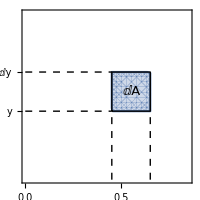

```mathematica
s=0.15;s2=0.22;
centerPlot@Show[RegionPlot[0.45<x<0.65&&0.35<y<0.55,{x,0,1},{y,0,1}(*,FrameLabel->(font[#,Italic]&/@{"x","y"})*),PlotRange->0.85{{0,1},{0,1}},ImageSize->200,PlotRangePadding->None,FrameTicks->{{{{0.35,font["y",12]},{0.55,font["y+ⅆy",12]}},None},{{{0.45,font["x",12]},{0.65,font["x+ⅆx",12]},None},{None}}}],
Graphics[{{Thick,Line[{{0.45,0.35},{0.45,0.55},{0.65,0.55},{0.65,0.35},{0.45,0.35}}]},{Dashed,Line[{{{0.45,0},{0.45,0.35}},{{0.65,0},{0.65,0.35}},{{0,0.35},{0.45,0.35}},{{0,0.55},{0.45,0.55}}}]},Text[font["ⅆA",13],{0.55,0.45}]}]]
```

The situation is the same for polar coordinates, although perhaps slightly less familiar. Consider a generic point (r,θ) and the infinitesimally displaced points found when we vary the first coordinate by ⅆr and the second coordinate by ⅆθ. Thus we have four points (r,θ), (r+ⅆr,θ), (r,θ+ⅆθ), and (r+ⅆr,θ+ⅆθ). As shown in the figure below, the element of this infinitesimal area equals (ⅆr)(rⅆθ)=r ⅆrⅆθ. Thus,

Polar Coordinate Area Element ⅆA=rⅆrⅆθ

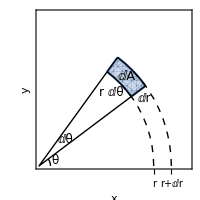

```mathematica
s=0.15;s2=0.22;
centerPlot@Show[RegionPlot[0.65^2<x^2+y^2<0.75^2&&π/4-s<ArcTan[y,x]<π/4+s,{x,0,1},{y,0,1},FrameLabel->(font[#,Italic]&/@{"x","y"}),PlotRange->0.85{{0,1},{0,1}},ImageSize->200,PlotRangePadding->None,FrameTicks->{{None,None},{{{0.65,font["r",12]},{0.75,font["r+ⅆr",12]}},None}}],
Graphics[{(*Arrow[{{{0,0},{1,0}},{{0,0},{0,1}}}],*)Line[{{0.65Cos[π/4+s],0.65Sin[π/4+s]},{0,0},{0.65Cos[π/4-s],0.65Sin[π/4-s]}}],Circle[{0,0},0.065,{π/4-s,0}],{Thick,Circle[{0,0},0.65,{π/4-s,π/4+s}],Circle[{0,0},0.75,{π/4-s,π/4+s}],Line[{{0.65Cos[π/4-s],0.65Sin[π/4-s]},{0.75Cos[π/4-s],0.75Sin[π/4-s]}}],Line[{{0.65Cos[π/4+s],0.65Sin[π/4+s]},{0.75Cos[π/4+s],0.75Sin[π/4+s]}}]},{Dashed,Circle[{0,0},0.65,{0,π/4}],Circle[{0,0},0.75,{0,π/4}]},Text[font["θ",12],{0.09,0.028}],Text[font["ⅆθ",12],{0.15,0.145}],Text[font["r ⅆθ",12],0.58{Cos[π/4],Sin[π/4]}],Text[font["ⅆr",12],0.705{Cos[π/4-s2],Sin[π/4-s2]}],Text[font["ⅆA",13],0.7{Cos[π/4],Sin[π/4]}]}]]
```

What does this imply? If we integrate f[r,θ] over a region in polar coordinates, then the integral must take the form

∫∫f[r,θ]rⅆrⅆθ

Example
Compute the area of a region R enclosed by the curve r̃[θ] and the rays θ=a and θ=b where 0<b-a≤2π.

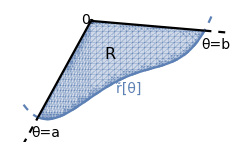

```mathematica
func=48.61611799153571+0.609315220905096 x-0.003907805365856481 x^2-0.000013313926866589077 x^3+3.627112231902089*^-7 x^4+1.4191338039077048*^-10 x^5+1.5031095980247882*^-12 x^6;
func2=200.73904261906205+2.024634753968737 x;
func3=137.13728021679154-0.09542399277361452 x;
centerPlot@Show[Plot[func,{x,-119,130},PlotStyle->Dashed,Axes->False,PlotRange->{{-120,150},{-35,150}},ImageSize->250],Plot[func,{x,-100,120}],RegionPlot[(func/.x->xx)<yy&&(func2/.x->xx)>yy,{xx,-100,-30},{yy,-10,140},BoundaryStyle->None],RegionPlot[(func/.x->xx)<yy&&(func3/.x->xx)>yy,{xx,-30,120},{yy,-10,140},BoundaryStyle->None],Plot[func2,{x,-100,-30},PlotStyle->Black],Plot[func2,{x,-120,-100},PlotStyle->{Black,Dashed}],Plot[func3,{x,-30,120},PlotStyle->Black],Plot[func3,{x,120,150},PlotStyle->{Black,Dashed}],Graphics[{PointSize[0.015],Point[{-30,140}],Text[font["R",16,Italic],{-5,90}],Text[font["0",14],{-37,142}],Text[font["θ=a",14],{-90,-25}],Text[font["θ=b",14],{135,105}],Text[font["r̃[θ]",14,color1],{20,40}]}]]
```

Solution
To compute an area, we set f[r,θ]=1 in Equation (TextNumbered) and find the area

∫_a^b ∫_0^(r̃[θ]) rⅆrⅆθ=1/2∫_a^b (r̃[θ])^2 ⅆθ

which is a famous formula for area in polar coordinates. □

Example
Find the area of an ellipse with semi-major axis a and semi-minor axis b.

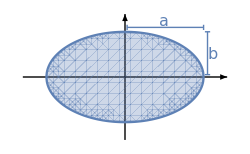

```mathematica
a=0.1;
centerPlot@Show[Graphics[{Arrowheads[0.04],
Arrow[3.9{{{-1,0},{1,0}},1/GoldenRatio{{0,-1},{0,1}}}],{color1,Line[{{{0.08,1.9},{3,1.9}},{{0.08,1.9+a},{0.08,1.9-a}},{{3,1.9+a},{3,1.9-a}},{{3.15,0.09},{3.15,√3}},{{3.15-a,0.09},{3.15+a,0.09}},{{3.15-a,√3},{3.15+a,√3}}}],Text[font["a",16,Italic],{3/2,2.13}],Text[font["b",16,Italic],{3.35,√3/2}]}},ImageSize->250],RegionPlot[x^2/9+y^2/3<1,{x,-4,4},{y,-4,4}]]
```

Solution
Orienting our ellipse as in the figure above, the equation of an ellipse is

x^2/a^2+y^2/b^2=1

In polar coordinates (x=r Cos[θ], y=r Sin[θ]) this becomes

(r^2 Cos[θ]^2)/a^2+(r^2 Sin[θ]^2)/b^2=1

Method 1: Integrate using Polar Coordinates
As shown in the previous Example, the area of the ellipse equals 1/2∫_0^(2π) (r̃[θ])^2 ⅆθ where r̃[θ] traces the boundary of the ellipse. From Equation (TextNumbered),

(r̃[θ])^2=1/(Cos[θ]^2/a^2+Sin[θ]^2/b^2)=(a^2 b^2)/(b^2 Cos[θ]^2+a^2 Sin[θ]^2)

Integrating over the top-half of the ellipse and multiplying by 2 (for the bottom half), the area of the ellipse equals

∫_0^π (a^2 b^2)/(b^2 Cos[θ]^2+a^2 Sin[θ]^2)ⅆθ=a b ArcTan[(a Sin[θ])/(b Cos[θ])]_(θ=0)^(θ=π)=π a b-0=π a b

You must be very careful when taking the bounds on this integral, because of the branch cuts (i.e. the discontinuities) in ArcTan. When taking the bounds on this integral you must take the modulus of the ArcTan function so that it becomes continuous. Moral of the story: Check your answer with Mathematica (but note that even with Mathematica it is easy to get mixed up about the ArcTan branch cuts!)

```mathematica
Integrate[(a^2 b^2)/(b^2 Cos[θ]^2+a^2 Sin[θ]^2),{θ,0,π},Assumptions->0<b<a]
```

a b π

Method 2: Integrate using Cartesian Coordinates
Using the equation of an ellipse

x^2/a^2+y^2/b^2=1

we can integrate over the top-half of the ellipse in Cartesian coordinates (multiplying by 2 to account for the bottom half)

2∫_-a^a (b(1-x^2/a^2))^(1/2)=b {x (1-x^2/a^2)^(1/2)+a ArcSin[x/a]}_(x=-a)^(x=a)=a b (π/2-(-π/2))=π a b

This integral is nasty, so you probably won’t tackle the problem this way without Mathematica at your back. However, it is nice to check that this method yields the same answer.

Method 3: A Clever Trick
By far the easiest way to find the area of an ellipse is to note that the equation

x^2/a^2+y^2/b^2=1

becomes a circle if we stretch our coordinate system in the y-direction using the transformation ỹ=a/b y,

x^2/a^2+(ỹ)^2/a^2=1

This is the equation of a circle of radius a, and therefore of area π a^2. An infinitesimal unit of area in our normal coordinates, ⅆxⅆy, is related to the infinitesimal unit of area in the new coordinates, ⅆxⅆy=b/a ⅆxⅆ ỹ. In other words, any area that we measure in the x-y coordinate system is given by  a/b times the area measured in the x-ỹ coordinate system, which equals b/a(π a^2)=π a b. □

### 3D Spherical Coordinates

A generic 3D vector in Cartesian coordinates is

A⃗=A_x x̂+A_y ŷ+A_z ẑ

which in spherical polar coordinates is given by

A⃗=r Sin[θ] Cos[ϕ]x̂+r Sin[θ] Sin[ϕ]ŷ+r Cos[θ] ẑ

where ϕ∈[0,2π) is the polar angle and θ∈[0,π] is the azimuthal angle.

```mathematica
arc[r_,θ_,{ϕ1_, ϕ2_}]:=
Line[Table[r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{ϕ,ϕ1,ϕ2,(ϕ2-ϕ1)/Round[((ϕ2-ϕ1)/(2π))180.]}]]
arc[r_,{θ1_,θ2_},ϕ_]:=
Line[Table[r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
PolarToCartesian[{r_,θ_,ϕ_}]:=
r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]}
sphericalGraphic = With[{hemisphere = First[ParametricPlot3D[
{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{ϕ,0,π/2},{θ,0,2π},Boxed->False,Mesh->None,Axes->None]],
al=1.2,
tl=1.35
},
Graphics3D[{
Arrowheads[Small],
Arrow[al{{{-1,0,0},{1,0,0}},{{0,-1,0},{0,1,0}},{{0,0,-.1/1.1},{0,0,1}}}],
Text[font["x",Italic],tl{1,0,0}],
Text[font["y",Italic],tl{0,1,0}],
Text[font["z",Italic],tl{0,0,1}],
With[{ϕ=45°,θ=45°,ar=.25,tr=.35},
{
{Arrow[{{0,0,0},PolarToCartesian[{1,θ,θ}]}]},
arc[1,ϕ,{0,θ}],
arc[Sin[θ],{0,ϕ},π/2],
Line[{{0,0,0},PolarToCartesian[{Sin[θ],ϕ,π/2}],
PolarToCartesian[{1,ϕ,θ}]}],
arc[ar,{0,ϕ},π/2],
arc[ar,ϕ,{0,θ}],
Text[font@"ϕ",PolarToCartesian[{tr,ϕ/2,π/2}]+{-0.15,0.005,0},{-1,1}],
Text[font@"θ",PolarToCartesian[{tr,θ,θ/2}]+{0,0,-0.08},{0,-1}]
}],
{Opacity[.5],hemisphere}
},Boxed->False,ViewPoint->{2.72,-0.92,1.78},ViewVertical->{0.07,-0.037,1.83}]
];
polarGraphic = With[{disk = First[ParametricPlot3D[
{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], 0},{ϕ,0,π/2},{θ,0,2π},Boxed->False,Mesh->None,Axes->None]],
al=1.2,
tl=1.3
},
Graphics3D[{
Arrowheads[Small],
{Style[Text["z",tl{0,0,1}],FontOpacity->0]},
Arrow[al{{{-1,0,0},{1,0,0}},{{0,-1,0},{0,1,0}}}],
Text[font["x",Italic],tl{1.05,0,0}],
Text[font["y",Italic],tl{0,1.05,0}],
With[{θ=45°,ϕ=45°,ar=.25,tr=.35},
{
arc[ar,{0,θ},π/2],
Arrow[{{0,0,0},PolarToCartesian[{Sin[ϕ],θ,π/2}]}],
Text[font["θ",13],PolarToCartesian[{tr,θ/2,π/2}]+{-0.12,0.02,0},{-1,1}],
Text[font["r",Italic],PolarToCartesian[{.4,θ,π/2}]+{0.07,0.02,0},{-1,-1}]
}],
{Opacity[.7],disk}
},Boxed->False,ViewPoint->{2.72,-0.92,1.78},ViewVertical->{0.07,-0.037,1.83}]
];
centerPlot@Row[Show[#,ImageSize->250]& /@ {polarGraphic,sphericalGraphic}]
```

-Graphics3D--Graphics3D-

Unfortunately, as seen above, physicists take the horrible convention where θ is the polar angle in 2D radial coordinates but ϕ is the polar angle in 3D spherical coordinates. Therefore, to regain polar coordinates from spherical coordinates you must set θ=π/2 and then rename ϕ=θ. (Mathematicians, on the other hand, tend to switch the definitions of θ and ϕ in spherical coordinates to avoid this issue!)

We can convert from Cartesian coordinates to spherical coordinates using

r=√(A_x^2+A_y^2+A_z^2)

θ=ArcTan[((A_x^2+A_y^2)^(1/2))/A_z]=ArcCos[A_z/((A_x^2+A_y^2+A_z^2)^(1/2))]

ϕ=ArcTan[A_y/A_x]

(I encourage you to verify that both of these expressions for θ are equal!)

Example
Staying on a sphere of radius R, what is the shortest distance between the point (0,0,R) on the z-axis and a general point (x,y,z) on the sphere?

```mathematica
θ=0.6;
colors={RGBColor[0, 0.38, 0.1],RGBColor[0, 0.52, 1]};
pnts=Table[1.05{Sin[θθ],0,Cos[θθ]},{θθ,0,θ,0.01}];
centerPlot@Graphics3D[{Sphere[],PointSize[0.02],{colors[[1]],Point[1.05{{0,0,1},{Sin[θ],0,Cos[θ]}}]},{colors[[2]],Line[pnts]},Text[font["(0,0,R)"],{0,0,1.3}],Text[font["(x,y,z)"],1.3{Sin[θ],0,Cos[θ]}+{0.1,0,0}]},Boxed->False,PlotRangePadding->None,ImageSize->{151.24999999999815,168.75},PlotRangePadding->None,ViewAngle->0.28134970767492745]
```

-Graphics3D-

Solution
Rewrite the point (x,y,z) in spherical coordinates as (R,θ,ϕ) where θ=ArcTan[((x^2+y^2)^(1/2))/z] and ϕ=ArcTan[y/x] are given by Equations (TextNumbered) and (TextNumbered). Note that the shortest distance on a sphere is given by an arc along a great circle, that is, a circle whose center lies at the center of the sphere. In this case, the arc can be parameterized in spherical coordinates as (R,θ',ϕ) where θ'∈[0,θ] moves you from the point on the z-axis to the point of interest.

```mathematica
θ=0.6;
colors={RGBColor[0, 0.38, 0.1],RGBColor[0, 0.52, 1]};
pnts=Table[1.05{Sin[θθ],0,Cos[θθ]},{θθ,0,θ,0.01}];
centerPlot@Graphics3D[{{Line[{{0,0,1},{0,0,0},{Sin[θ],0,Cos[θ]}}]},{Opacity[0.7],Sphere[]},PointSize[0.02],{colors[[1]],Point[1.05{{0,0,1},{Sin[θ],0,Cos[θ]}}]},{colors[[2]],Line[pnts]},Text[font["(0,0,R)"],{0,0,1.3}],Text[font["(x,y,z)"],1.3{Sin[θ],0,Cos[θ]}+{0.1,0,0}],Text[font["θ"],0.2{Sin[θ],0,Cos[θ]}+{-0.03,0,0.1}]},Boxed->False,PlotRangePadding->None,ImageSize->{151.24999999999815,168.75},PlotRangePadding->None,ViewAngle->0.28134970767492745]
```

-Graphics3D-

Therefore, the shortest distance between these two point while staying on the sphere is given by the length of this arc, which is

R θ=R ArcTan[((x^2+y^2)^(1/2))/z]

We can quickly check some limits. When z=R and x=y=0, we correctly find the distance to be zero. When z=-R and x=y=0, you have to be more careful since ArcTan[0]=0, but this value is not unique since Tan[0]=Tan[π]=0, and indeed in this case θ=π. When z=0 and you are anywhere on the z=0 plane, the distance is given by R ArcTan[∞]=(R π)/2 which is one fourth the circumference of the sphere, as expected. □

### 3D Cylindrical Coordinates

Another 3D coordinate system that is occasionally convenient is cylindrical coordinates which has a radial distance ρ, a polar angle θ, and a height component z . Essentially, cylindrical coordinates extend 2D polar coordinates to 3D by adding the Euclidean height z. A vector A⃗=A_x x̂+A_y ŷ+A_z ẑ in Cartesian coordinates would be written in cylindrical coordinates as

A⃗=ρ Cos[θ]x̂+ρ Sin[θ]ŷ+z ẑ

where θ∈[0,2π) is the polar angle.

```mathematica
arc[r_,θ_,{ϕ1_, ϕ2_}]:=
Line[Table[r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{ϕ,ϕ1,ϕ2,(ϕ2-ϕ1)/Round[((ϕ2-ϕ1)/(2π))180.]}]]
arc[r_,{θ1_,θ2_},ϕ_]:=
Line[Table[r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
PolarToCartesian[{r_,θ_,ϕ_}]:=
r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]}
cylindricalGraphic = With[{
al=1.2,
tl=1.35,
height=0.85
},
cyl1 = First[ParametricPlot3D[
{0.8 Sin[ϕ] Cos[θ],0.8 Sin[ϕ] Sin[θ], height},{ϕ,0,π/2},{θ,0,2π},Boxed->False,Mesh->None,Axes->None]];
cyl2 = First[ParametricPlot3D[
{0.8 Cos[θ],0.8 Sin[θ],zz},{zz,0,height},{θ,0,2π},Boxed->False,Mesh->None,Axes->None]];
centerPlot@Graphics3D[{
Arrowheads[Medium],
Arrow[al{{{-1,0,0},{1,0,0}},{{0,-1,0},{0,1,0}},{{0,0,-.1/1.1},{0,0,1}}}],
Text[font["x",Italic],tl{1,0,0}],
Text[font["y",Italic],tl{0,1,0}],
Text[font["z",Italic],tl{0,0,1}],
With[{θ=45°,ar=.25,tr=.25,z=0.35,ρ=0.65},
{
PointSize[0.02],{RGBColor[0.32, 0., 0.51],Point[0.99{ρ Cos[θ],ρ Sin[θ],z}]},
arc[ρ,{0,θ},π/2],Line[{{{0,0,z},{ρ Cos[θ],ρ Sin[θ],z}},{{0,0,0},{ρ Cos[θ],ρ Sin[θ],0}},{{ρ Cos[θ],ρ Sin[θ],0},{ρ Cos[θ],ρ Sin[θ],z}}}],
arc[ar,{0,θ},π/2],
Text[font@"θ",{tr Cos[θ/2],tr Sin[θ/2],0}+{0,0,0.035},{-1,1}],
Text[font["z",Italic],{(ρ+0.08) Cos[θ],(ρ+0.08) Sin[θ],z/2}+{0,0,0.04}],
Text[font["ρ"],{ρ/2 Cos[θ],ρ/2 Sin[θ],z}+{0,0,0.0},{0,-1}]
}],
{Opacity[.7],cyl1,cyl2}
},Boxed->False,ViewPoint->{2.8787694864121054,-0.8743808538009489,1.501014445836184},ViewVertical->{0.022146876875507985,-0.006437778851452326,1.7471986729777156},ImageSize->250]
]
```

-Graphics3D-

We can convert from Cartesian coordinates to cylindrical coordinates using

ρ=√(A_x^2+A_y^2)

θ=ArcTan[A_y/A_x]

z=A_z

## Mathematica Initialization

```mathematica
colors={color1,color2,color3,color4}=ColorData[97][#]&/@{1,10,5,6};
```

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```